# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup

```mathematica
nv=3;
nh=1;

volExp=14;
cdir="../../"<>getCacheDirRaw[volExp];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

# Import data

## Import cache and transformations

```mathematica
SetDirectory[NotebookDirectory[]];
cdir="../../"<>getCacheDirRaw[volExp];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{1749.78,6454.46,2550.},{1392.37,5856.93,2450.}}

```mathematica
SetDirectory[NotebookDirectory[]];

noIP3Rs={100,500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};
(*
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};
*)
ip3s={
"ip3_0p100","ip3_0p400","ip3_0p700","ip3_1p000",
"ip3_1p300","ip3_1p600","ip3_1p900"
};

ip3Keys={};
Do[
Do[
AppendTo[ip3Keys,{noIP3R,ip3}]
,{ip3,ip3s}];
,{noIP3R,noIP3Rs}];

filtered0=Association[];
derivs0=Association[];

Monitor[
Do[
{noIP3R,ip3}=ip3Keys[[iKey]];
cdir="../../"<>getCacheDirRaw[volExp,noIP3R];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"filtered0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

filtered0[ip3Keys[[iKey]]]=makePStructFromLFDL[nv,nh,pLFDL];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"derivs0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

derivs0[ip3Keys[[iKey]]]=makePStructFromLFDL[nv,nh,pLFDL];

,{iKey,Length[ip3Keys]}];
,ProgressIndicator[iKey,{1,Length[ip3Keys]}]];
```

## Viz

```mathematica
pltEvery=20;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
colors2=Table[ColorData["BrownCyanTones"][i/Length[noIP3Rs]],{i,Length[noIP3Rs]}]
```

{RGBColor[0.584692, 0.44694657142857147, 0.3233],RGBColor[0.756208, 0.6565245714285715, 0.5653625714285714],RGBColor[0.8283884285714286, 0.8146152857142858, 0.7674522857142857],RGBColor[0.7939004285714286, 0.9150341428571429, 0.9120654285714286],RGBColor[0.6742975714285715, 0.9295297142857143, 0.965857],RGBColor[0.5239352857142857, 0.863684, 0.9428224285714286],RGBColor[0.342992, 0.650614, 0.772702]}

{RGBColor[0.46120126666666666, 0.31681180000000003, 0.1953522],RGBColor[0.5718082666666666, 0.43211746666666667, 0.30652666666666667],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.7420352, 0.6337242666666667, 0.5369025333333334],RGBColor[0.79164, 0.7135253333333333, 0.6365126666666666],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8324740666666667, 0.8510343333333333, 0.8162937333333333],RGBColor[0.8163796666666667, 0.8978964666666667, 0.8837798666666666],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7212263333333333, 0.934652, 0.9583823333333333],RGBColor[0.6555260666666667, 0.9274808, 0.9688468666666666],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.5136983333333334, 0.8581725333333334, 0.9402766],RGBColor[0.42925813333333335, 0.7587398666666667, 0.8608870666666667],RGBColor[0.342992, 0.650614, 0.772702]}

## Vals

```mathematica
pltParams[params0_,noIP3R_,k_]:=Module[
{rngs,r,ip3,ip3Key,xPlt}
,
rngs=<|
"wt11"->{0,1.4},
"b1"->{-1.2,2.0},
"b3"->{-1.5,1.5}
|>;

r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=params0[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->rngs[k],
PlotLabel->ToString[noIP3R]<>" "<>labels[k],
FrameLabel->{"Time (s)"}
];
Return[r];
];
```

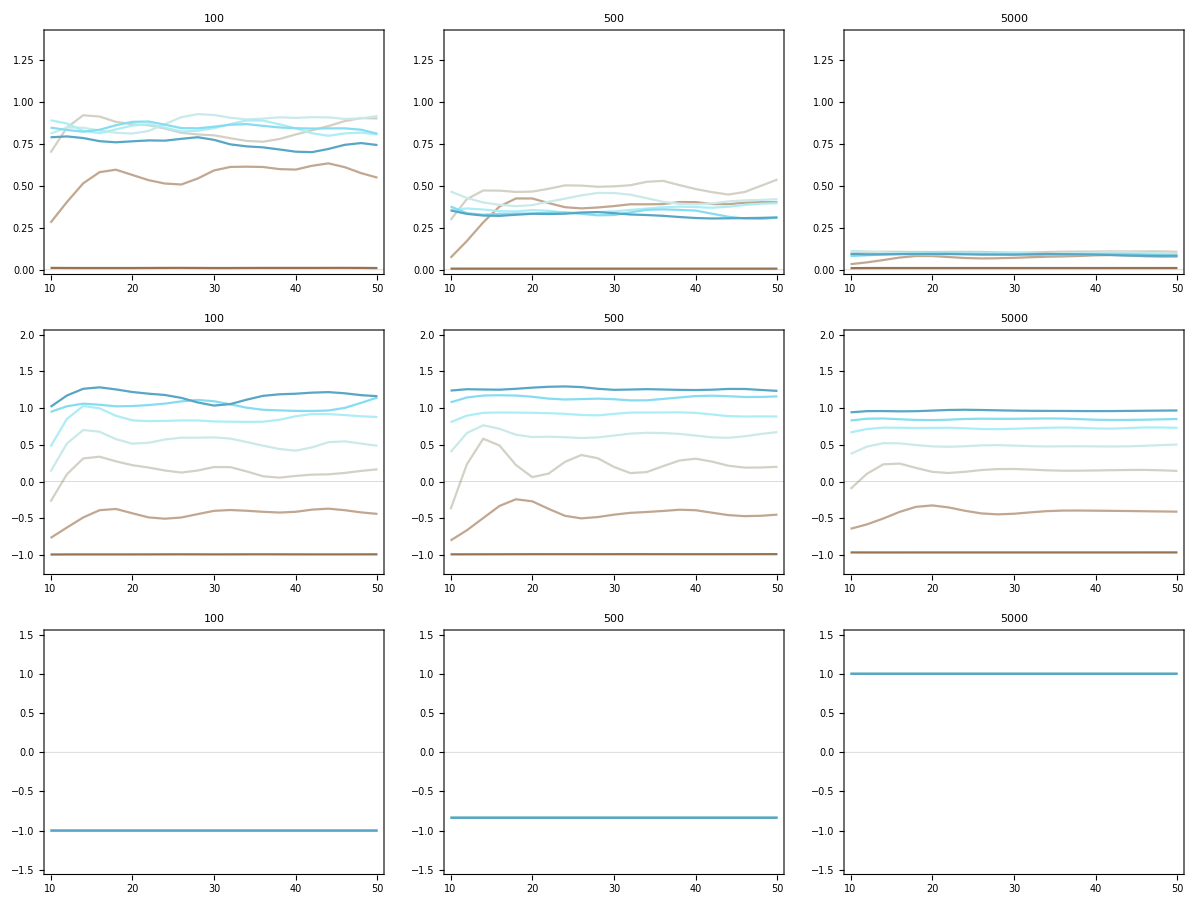

```mathematica
plts=Table[
Table[
pltParams[filtered0,noIP3R,k]
,{noIP3R,{100,500,5000}}]
,{k,{"wt11","b1","b3"}}];
p=Grid[plts]
```

## Derivs

```mathematica
pltTVR[derivs_,noIP3R_,k_]:=Module[
{r,ip3,ip3Key,xPlt,rng}
,
If[k=="wt11",
rng={-0.005,0.01},
rng={-0.04,0.06}
];

r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
 xPlt=derivs[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt[[;;-2]],xPlt}],PlotRange->All,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->rng,
PlotLabel->"TVR deriv: "<>labels[k]<>" "<>ToString[noIP3R],
FrameLabel->{"Time (s)"}
];
Return[r];
]
```

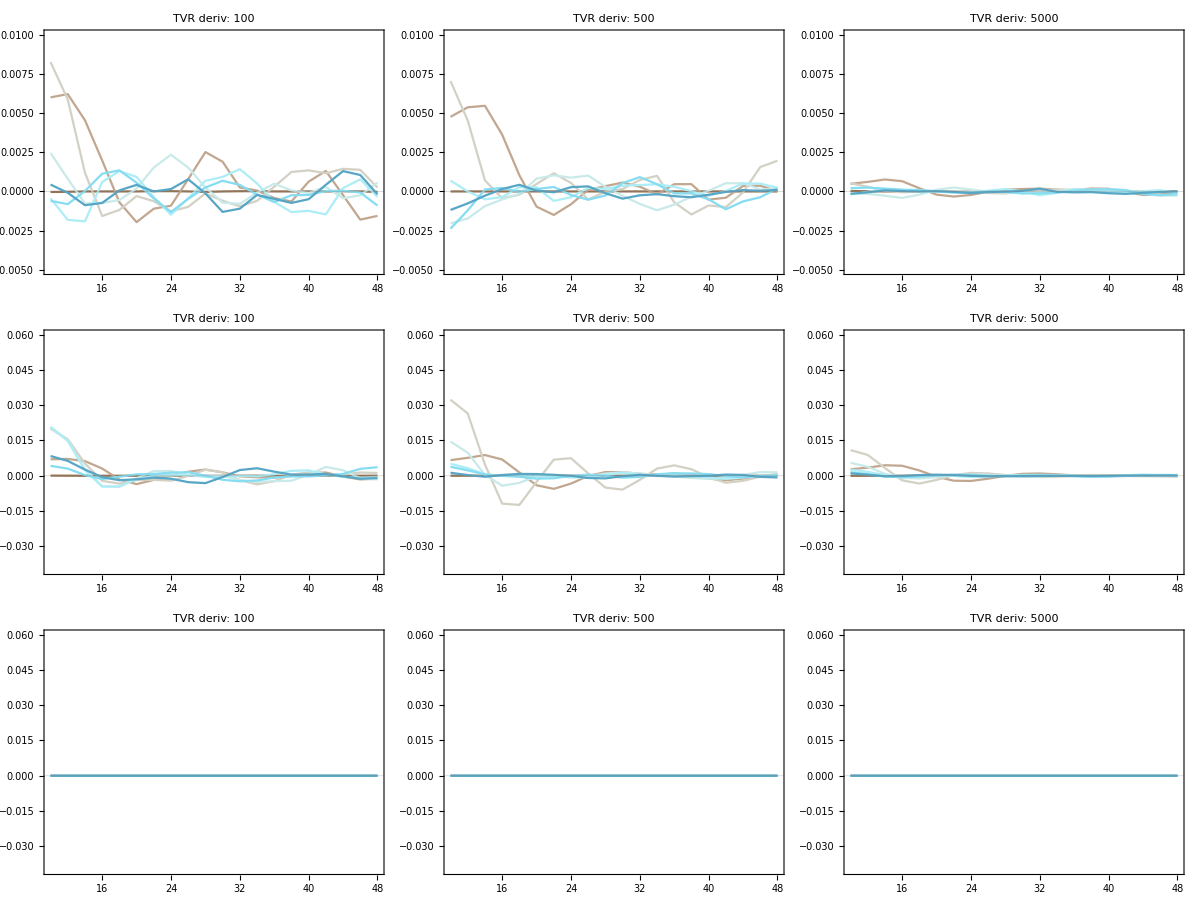

```mathematica
plts=Table[
Table[
pltTVR[derivs0,noIP3R,k]
,{noIP3R,{100,500,5000}}]
,{k,{"wt11","b1","b3"}}];
p=Grid[plts]
```

# Import graphs

```mathematica
modes={"rxns","params"};

SetDirectory[NotebookDirectory[]];
graphInputsWOSTD=Association[];
graphCalculateSTDs=Association[];
Do[
graphInputsWOSTD[mode]=Import["training_data/graph_"<>mode<>"_inputs_wo_std.wlnet"];
graphCalculateSTDs[mode]=Import["training_data/graph_"<>mode<>"_calculate_stds.wlnet"];
,{mode,modes}];
```

# Make training data

## Funcs

```mathematica
calculateStdsMVRandom[ip3KeysTraining_,dataDesc_,filtered0_,graphCalculateSTDs_,nRand_]:=Module[
{noTrainingData,inputsWOSTD,f0,in,rxnsSTDm,rxnsSTDv,ip3Key,keysAll,keysUse,key,i,tpt}
,

noTrainingData=Length[ip3KeysTraining]*dataDesc["noTpts"];
Print["Using ", nRand, " random pts out of ",noTrainingData," to estimate std params"];

keysAll=Flatten[Table[Table[{ip3Key,tpt},{tpt,dataDesc["noTpts"]}],{ip3Key,ip3KeysTraining}],1];
keysUse=RandomSample[keysAll,nRand];

inputsWOSTD=ConstantArray[0,nRand];

Monitor[
Do[
key=keysUse[[i]];
{ip3Key,tpt}=key;

f0=filtered0[ip3Key]["LD"];
in=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->f0[[tpt]]["sig2"],
"tpt"->tpt
|>;
inputsWOSTD[[i]]=graphCalculateSTDs[in];

,{i,Length[keysUse]}];
,ProgressIndicator[i,{1,Length[keysUse]}]];

rxnsSTDm=Mean[inputsWOSTD];
rxnsSTDv=StandardDeviation[inputsWOSTD];

rxnsSTDm=Table[If[Abs[x]<10^-3,0.0,x],{x,rxnsSTDm}];
rxnsSTDv=Table[If[Abs[x]<10^-3,1.0,x],{x,rxnsSTDv}];

Return[{rxnsSTDm,rxnsSTDv}]
]
```

```mathematica
calculateStdsMV[ip3KeysTraining_,dataDesc_,filtered0_,graphCalculateSTDs_]:=Module[
{noTrainingData,inputsWOSTD,idx,f0,in,rxnsSTDm,rxnsSTDv,ip3Key}
,

noTrainingData=Length[ip3KeysTraining]*dataDesc["noTpts"];
inputsWOSTD=ConstantArray[0,noTrainingData];

idx=1;
Monitor[
Do[
ip3Key=ip3KeysTraining[[i]];

f0=filtered0[ip3Key]["LD"];
Do[
in=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->f0[[tpt]]["sig2"],
"tpt"->tpt
|>;
inputsWOSTD[[idx]]=graphCalculateSTDs[in];

idx+=1;
,{tpt,dataDesc["noTpts"]}];
,{i,Length[ip3KeysTraining]}];
,ProgressIndicator[i,{1,Length[ip3KeysTraining]}]];

rxnsSTDm=Mean[inputsWOSTD];
rxnsSTDv=StandardDeviation[inputsWOSTD];

rxnsSTDm=Table[If[Abs[x]<10^-3,0.0,x],{x,rxnsSTDm}];
rxnsSTDv=Table[If[Abs[x]<10^-3,1.0,x],{x,rxnsSTDv}];

Return[{rxnsSTDm,rxnsSTDv}]
];
```

```mathematica
makeTrainingData[ip3Keys_,noTpts_,derivs0_,filtered0_]:=Module[
{trainingData,idx,d0,f0,d0v}
,
trainingData=ConstantArray[0,Length[ip3Keys]*(noTpts-1)];

idx=1;
Do[
d0=derivs0[ip3Key]["LD"];
f0=filtered0[ip3Key]["LD"];
Do[
d0v=Flatten[{d0[[tpt]]["b"],d0[[tpt]]["wt"],d0[[tpt]]["sig2"]}];

(* Zero *)
d0v=d0v[[{1,4}]];

trainingData[[idx]]=<|
"wt"->f0[[tpt]]["wt"],
"b"->f0[[tpt]]["b"],
"sig2"->{f0[[tpt]]["sig2"]},
"Output"->d0v,
"tpt"->{tpt}
|>;
idx+=1;
,{tpt,noTpts-1}];
,{ip3Key,ip3Keys}];

Return[trainingData];
]
```

```mathematica
standardizeTraining[data_]:=Module[
{out,dataS,outMean,outStd,zeroCutoff,y}
,
out=Table[x["Output"],{x,data}];
outMean=Mean[out];
outStd=StandardDeviation[out];

zeroCutoff=10^-6;
outMean=Table[If[Abs[x]<zeroCutoff,0.0,x],{x,outMean}];
outStd=Table[If[Abs[x]<zeroCutoff,1.0,x],{x,outStd}];

dataS=Table[
y=x;
y["Output"]=(y["Output"]-outMean)/outStd;
y
,{x,data}];

Return[{dataS,outMean,outStd}]
]
```

```mathematica
standardizeValidation[data_,outMean_,outStd_]:=Module[
{dataS,y}
,
dataS=Table[
y=x;
y["Output"]=(y["Output"]-outMean)/outStd;
y
,{x,data}];

Return[dataS]
]
```

## Calculate STDs & export

## Training

```mathematica
ip3s
```

{ip3_0p100,ip3_0p400,ip3_0p700,ip3_1p000,ip3_1p300,ip3_1p600,ip3_1p900}

```mathematica
noIP3RsTraining={500,600,700,800,900,1000};

ip3KeysTraining={};
Do[
ip3sTrain=ip3s;

Do[
AppendTo[ip3KeysTraining,{noIP3R,ip3}];
,{ip3,ip3sTrain}];
,{noIP3R,noIP3RsTraining}];
Clear[ip3sTrain];

SetDirectory[NotebookDirectory[]];
Export["training_data/ip3_keys_train.txt",ip3KeysTraining,"Table","FieldSeparators"->" "];

Do[

nRand=4000;
{rxnsSTDm,rxnsSTDv}=calculateStdsMVRandom[ip3KeysTraining,dataDesc,filtered0,graphCalculateSTDs[mode],nRand];

SetDirectory[NotebookDirectory[]];
Export["training_data/std_"<>mode<>"_m.txt",rxnsSTDm,"Table","FieldSeparators"->" "];
Export["training_data/std_"<>mode<>"_v.txt",rxnsSTDv,"Table","FieldSeparators"->" "];
,{mode,modes}];
```

Using 4000 random pts out of 16842 to estimate std params

Using 4000 random pts out of 16842 to estimate std params

## Validation

```mathematica
noIP3RsValidation={2000,3500,5000};

ip3KeysValidation={};
Do[
ip3sValidate=ip3s;

Do[
AppendTo[ip3KeysValidation,{noIP3R,ip3}];
,{ip3,ip3sValidate}];
,{noIP3R,noIP3RsValidation}];
Clear[ip3sValidate];

SetDirectory[NotebookDirectory[]];
Export["training_data/ip3_keys_test.txt",ip3KeysValidation,"Table","FieldSeparators"->" "];
```

## Make training data

```mathematica
trainingData=makeTrainingData[ip3KeysTraining,dataDesc["noTpts"],derivs0,filtered0];
validationData=makeTrainingData[ip3KeysValidation,dataDesc["noTpts"],derivs0,filtered0];
 
Length[trainingData]
Length[validationData]
noOutput=Length[trainingData[[1]]["Output"]]
```

16800

8400

2

## Scale & export

{0.000491846,0.000106781}

{0.0039937,0.000907487}

training_data/out_mean.txt

training_data/out_std.txt

training_data/training_data_s.mx

training_data/validation_data_s.mx

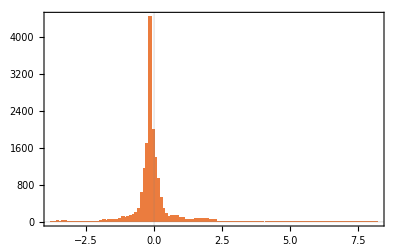
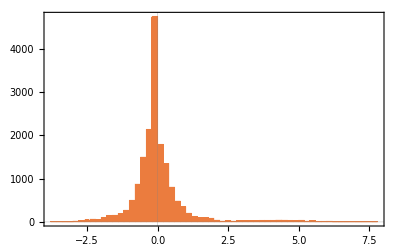

```mathematica
{trainingDataS,outMean,outStd}=standardizeTraining[trainingData];
outMean
outStd

validationDataS=standardizeValidation[validationData,outMean,outStd];

SetDirectory[NotebookDirectory[]];
Export["training_data/out_mean.txt",outMean,"Table","FieldSeparators"->" "]
Export["training_data/out_std.txt",outStd,"Table","FieldSeparators"->" "]

Export["training_data/training_data_s.mx",trainingDataS]
Export["training_data/validation_data_s.mx",validationDataS]

Table[
Histogram[Table[x["Output"][[i]],{x,trainingDataS}],PlotRange->All]
,{i,noOutput}]
```